# The convexity of beta density

In this document, we prove that f_2^-1(f) is convex, where f(α,β,x) is the beta density function, f_2^-1 is the inverse of the right branch, assuming that β>α>1.

## Beta density

```mathematica
f[α_,β_,x_]=PDF[BetaDistribution[α,β],x]
```

Piecewise[{{((1-x)^(-1+β) x^(-1+α))/Beta[α,β], 0<x<1}, {0, True}}]

We only need f for x ∈(0,1).

```mathematica
f0[α_,β_,x_]=Evaluate[f[α,β,x]//Simplify[#,0<x<1]&]
```

((1-x)^(-1+β) x^(-1+α))/Beta[α,β]

```mathematica
df=D[f0[α,β,x],x]
```

((1-x)^(-1+β) x^(-2+α) (-1+α))/Beta[α,β]-((1-x)^(-2+β) x^(-1+α) (-1+β))/Beta[α,β]

Let’s find m.

```mathematica
df*Beta[α,β]==0//Simplify
```

(1-x)^(-1+β) x^(-1+α) (-1+α-x (-2+α+β))==0

```mathematica
msol=Reduce[%&&0<x<1&&β>α>1,x,Reals]
```

β>1&&1<α<β&&x==(-1+α)/(-2+α+β)

This is the peak of the density.

```mathematica
m[α_,β_]=Evaluate[msol[[3,-1]]]
```

(-1+α)/(-2+α+β)

## An example

We try an example. This can be skipped.

```mathematica
a0=3;b0=7;
```

```mathematica
f1[x_]:=f0[a0,b0,x];
```

```mathematica
m1=m[a0,b0]
```

1/4

```mathematica
y1=f1[m1]
```

45927/16384

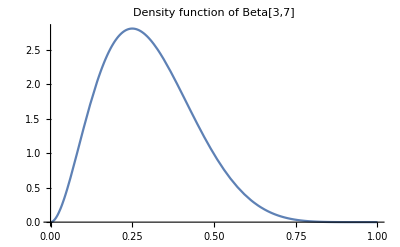

```mathematica
Plot[f1[x],{x,0,1},GridLines->{{m1}, {y1}},PlotLabel->"Density function of Beta[3,7]"]
```

Looks right. Let’s find the inverse on both side.

```mathematica
sol1=Reduce[f1[x]==y&&0<x<1,x,Reals]
```

(0<y<45927/16384&&(x==Root[-y+252 #1^2-1512 #1^3+3780 #1^4-5040 #1^5+3780 #1^6-1512 #1^7+252 #1^8&,2]||x==Root[-y+252 #1^2-1512 #1^3+3780 #1^4-5040 #1^5+3780 #1^6-1512 #1^7+252 #1^8&,3]))||(y==45927/16384&&x==1/4)

We get the two inverse, f_1^-1 for the left, f_2^-1 for the right.

```mathematica
fi1[y_]=sol1[[1,2,1,-1]]
```

Root[-y+252 #1^2-1512 #1^3+3780 #1^4-5040 #1^5+3780 #1^6-1512 #1^7+252 #1^8&,2]

```mathematica
fi2[y_]=sol1[[1,2,2,-1]]
```

Root[-y+252 #1^2-1512 #1^3+3780 #1^4-5040 #1^5+3780 #1^6-1512 #1^7+252 #1^8&,3]

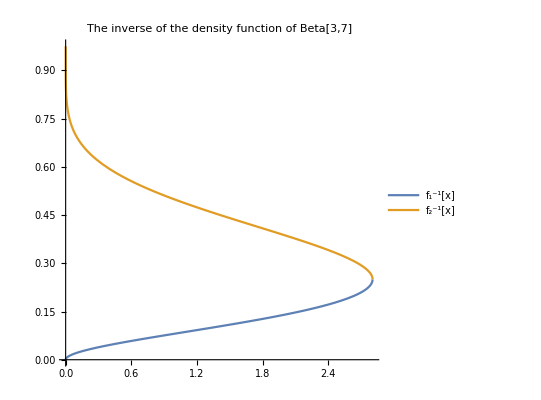

```mathematica
Plot[{fi1[y],fi2[y]},{y,0,y1},PlotLegends->{"f_1^-1[x]","f_2^-1[x]"},AspectRatio->1,PlotLabel->"The inverse of the density function of Beta[3,7]"]
```

So we want this function to be convex on (0,1/4).

```mathematica
r1[x_]:=Piecewise[{{fi1[f1[x]],1≥x≥m1},{fi2[f1[x]],0≤x<m1}}];
```

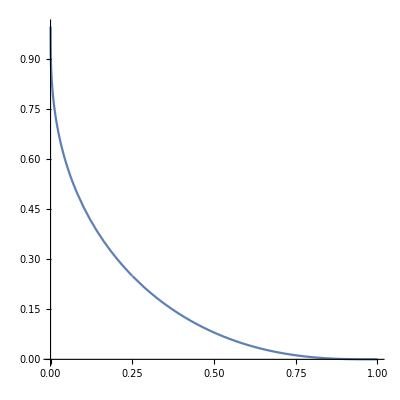

```mathematica
Plot[r1[x]//N[#,30]&,{x,0,1},PlotRange->All,AspectRatio->1,GridLines->{{m1}, {m1}}]
```

It’s obviously convex.

## Let’s prove this symbolically

### The derivative

```mathematica
ff[x_]:=f0[α,β,x]
```

The symbolic inverse is

```mathematica
gg=InverseFunction[ff]
```

ff^(-1)

Take 2nd derivative.

```mathematica
dr[0]=D[gg[ff[x]],{x,2}];
```

### Proof for α=3 and β=7

Can be skipped. Let’s just do the simple one.

```mathematica
dr[1]=dr[0]/.{α->3,β->7}
```

(504 (1-x)^6-6048 (1-x)^5 x+7560 (1-x)^4 x^2)/(504 (1-ff^(-1)[252 (1-x)^6 x^2])^6 ff^(-1)[252 (1-x)^6 x^2]-1512 (1-ff^(-1)[252 (1-x)^6 x^2])^5 (ff^(-1)[252 (1-x)^6 x^2])^2)-((504 (1-x)^6 x-1512 (1-x)^5 x^2) ((504 (504 (1-x)^6 x-1512 (1-x)^5 x^2) (1-ff^(-1)[252 (1-x)^6 x^2])^6)/(504 (1-ff^(-1)[252 (1-x)^6 x^2])^6 ff^(-1)[252 (1-x)^6 x^2]-1512 (1-ff^(-1)[252 (1-x)^6 x^2])^5 (ff^(-1)[252 (1-x)^6 x^2])^2)-(6048 (504 (1-x)^6 x-1512 (1-x)^5 x^2) (1-ff^(-1)[252 (1-x)^6 x^2])^5 ff^(-1)[252 (1-x)^6 x^2])/(504 (1-ff^(-1)[252 (1-x)^6 x^2])^6 ff^(-1)[252 (1-x)^6 x^2]-1512 (1-ff^(-1)[252 (1-x)^6 x^2])^5 (ff^(-1)[252 (1-x)^6 x^2])^2)+(7560 (504 (1-x)^6 x-1512 (1-x)^5 x^2) (1-ff^(-1)[252 (1-x)^6 x^2])^4 (ff^(-1)[252 (1-x)^6 x^2])^2)/(504 (1-ff^(-1)[252 (1-x)^6 x^2])^6 ff^(-1)[252 (1-x)^6 x^2]-1512 (1-ff^(-1)[252 (1-x)^6 x^2])^5 (ff^(-1)[252 (1-x)^6 x^2])^2)))/(504 (1-ff^(-1)[252 (1-x)^6 x^2])^6 ff^(-1)[252 (1-x)^6 x^2]-1512 (1-ff^(-1)[252 (1-x)^6 x^2])^5 (ff^(-1)[252 (1-x)^6 x^2])^2)^2

In this case we have the inverse functions, so we just plug them in.

```mathematica
dr[3][x_]=Piecewise[{{dr[1]/.InverseFunction[ff]->fi1,1≥x≥m1},{dr[1]/.InverseFunction[ff]->fi2,0≤x<m1}}];
```

Let’s first look at the left side.

```mathematica
dr[4]=dr[3][x]//Simplify[#,1≥x≥1/4]&
```

(6 (-1+x)^10 x^2 (x (-1+2 x)+Root[-x^2+6 x^3-15 x^4+20 x^5-15 x^6+6 x^7-x^8+#1^2-6 #1^3+15 #1^4-20 #1^5+15 #1^6-6 #1^7+#1^8&,2]-2 Root[-x^2+6 x^3-15 x^4+20 x^5-15 x^6+6 x^7-x^8+#1^2-6 #1^3+15 #1^4-20 #1^5+15 #1^6-6 #1^7+#1^8&,2]^2))/((-1+Root[-x^2+6 x^3-15 x^4+20 x^5-15 x^6+6 x^7-x^8+#1^2-6 #1^3+15 #1^4-20 #1^5+15 #1^6-6 #1^7+#1^8&,2])^11 Root[-x^2+6 x^3-15 x^4+20 x^5-15 x^6+6 x^7-x^8+#1^2-6 #1^3+15 #1^4-20 #1^5+15 #1^6-6 #1^7+#1^8&,2]^3 (-1+4 Root[-x^2+6 x^3-15 x^4+20 x^5-15 x^6+6 x^7-x^8+#1^2-6 #1^3+15 #1^4-20 #1^5+15 #1^6-6 #1^7+#1^8&,2])^3)

So the 2nd derivative is positive.

```mathematica
Reduce[dr[4]>0&&1>x>1/4,x,Reals]
```

1/4<x<1

Let’s look at the right side.

```mathematica
dr[5]=dr[3][x]//Simplify[#,1/4>x>0]&
```

(6 (-1+x)^10 x^2 (x (-1+2 x)+Root[-x^2+6 x^3-15 x^4+20 x^5-15 x^6+6 x^7-x^8+#1^2-6 #1^3+15 #1^4-20 #1^5+15 #1^6-6 #1^7+#1^8&,3]-2 Root[-x^2+6 x^3-15 x^4+20 x^5-15 x^6+6 x^7-x^8+#1^2-6 #1^3+15 #1^4-20 #1^5+15 #1^6-6 #1^7+#1^8&,3]^2))/((-1+Root[-x^2+6 x^3-15 x^4+20 x^5-15 x^6+6 x^7-x^8+#1^2-6 #1^3+15 #1^4-20 #1^5+15 #1^6-6 #1^7+#1^8&,3])^11 Root[-x^2+6 x^3-15 x^4+20 x^5-15 x^6+6 x^7-x^8+#1^2-6 #1^3+15 #1^4-20 #1^5+15 #1^6-6 #1^7+#1^8&,3]^3 (-1+4 Root[-x^2+6 x^3-15 x^4+20 x^5-15 x^6+6 x^7-x^8+#1^2-6 #1^3+15 #1^4-20 #1^5+15 #1^6-6 #1^7+#1^8&,3])^3)

```mathematica
Reduce[dr[5]>0&&1/4>x>0,x,Reals]
```

0<x<1/4

So we are done.

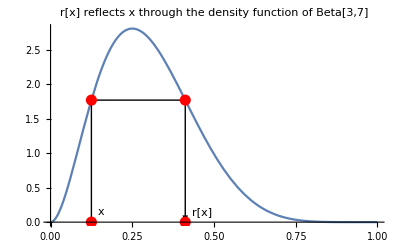

```mathematica
Module[{p,l,l1,pl,labels},
pl={{1/8,0},{1/8,f1[1/8]},{r1[1/8],f1[1/8]},{r1[1/8],0}};
p=Plot[f1[x],{x,0,1},PlotLabel->"r[x] reflects x through the density function of Beta[3,7]"];
l = Graphics[{Arrow[pl]}];
l1=ListPlot[pl,PlotStyle->Directive[Red,PointSize[.02]]];
labels={Text["x",pl[[1]]+{0.03,0.15}],Text["r[x]",pl[[4]]+{0.05,0.15}]};
Show[p,Graphics[{labels}],l,l1]]
```

## Genera Proof

### The first phase.

We reduce the problem to show that x+x1≥2 m[α,β], where x1 is the reflection of x.

We want the 2nd derivative to be positive when α<β. First simplify it a bit.

```mathematica
dd[0]=dr[0]//Simplify
```

((1-x)^(-4+β) x^(-4+α) (1-ff^(-1)[((1-x)^(-1+β) x^(-1+α))/Beta[α,β]])^(3-2 β) (ff^(-1)[((1-x)^(-1+β) x^(-1+α))/Beta[α,β]])^(3-2 α) (-(1-x) x (2-3 α+α^2-2 x (-1+α) (-3+α+β)+x^2 (6+α^2-5 β+β^2+α (-5+2 β))) (1-ff^(-1)[((1-x)^(-1+β) x^(-1+α))/Beta[α,β]])^(-1+β) (ff^(-1)[((1-x)^(-1+β) x^(-1+α))/Beta[α,β]])^(-1+α) (1-α+(-2+α+β) ff^(-1)[((1-x)^(-1+β) x^(-1+α))/Beta[α,β]])^2+(1-x)^β x^α (1-α+x (-2+α+β))^2 (2-3 α+α^2-2 (-1+α) (-3+α+β) ff^(-1)[((1-x)^(-1+β) x^(-1+α))/Beta[α,β]]+(6+α^2-5 β+β^2+α (-5+2 β)) (ff^(-1)[((1-x)^(-1+β) x^(-1+α))/Beta[α,β]])^2)))/(1-α+(-2+α+β) ff^(-1)[((1-x)^(-1+β) x^(-1+α))/Beta[α,β]])^3

Break it to terms and remove these that are positive. Note that ff^(-1)[((1-x)^(-1+β) x^(-1+α))/Beta[α,β]] is simply the reflection point of x, we replace it by x1 to make things look better.

```mathematica
dd[1]=dd[0]/.(ff^(-1))[((1-x)^(-1+β) x^(-1+α))/Beta[α,β]]->x1;
```

Break it to list of terms

```mathematica
List @@ dd[1]
```

{(1-x)^(-4+β),x^(-4+α),(1-x1)^(3-2 β),x1^(3-2 α),1/(1-α+x1 (-2+α+β))^3,-(1-x) x (1-x1)^(-1+β) x1^(-1+α) (1-α+x1 (-2+α+β))^2 (2-3 α+α^2-2 x (-1+α) (-3+α+β)+x^2 (6+α^2-5 β+β^2+α (-5+2 β)))+(1-x)^β x^α (1-α+x (-2+α+β))^2 (2-3 α+α^2-2 x1 (-1+α) (-3+α+β)+x1^2 (6+α^2-5 β+β^2+α (-5+2 β)))}

Get rid of some obviously positive terms (the first 4)

```mathematica
dd[3]=%[[5;;]]
```

{1/(1-α+x1 (-2+α+β))^3,-(1-x) x (1-x1)^(-1+β) x1^(-1+α) (1-α+x1 (-2+α+β))^2 (2-3 α+α^2-2 x (-1+α) (-3+α+β)+x^2 (6+α^2-5 β+β^2+α (-5+2 β)))+(1-x)^β x^α (1-α+x (-2+α+β))^2 (2-3 α+α^2-2 x1 (-1+α) (-3+α+β)+x1^2 (6+α^2-5 β+β^2+α (-5+2 β)))}

The first term of the left over is also positive.

```mathematica
assump=0<x<m[α,β]<x1<1&&β>α>1;
```

```mathematica
Reduce[dd[3][[1]]>0&&assump,x1,Reals]
```

β>1&&1<α<β&&0<x<(-1+α)/(-2+α+β)&&(-1+α)/(-2+α+β)<x1<1

Now only one left. We want it to be positive.

```mathematica
dd[4]=(dd[3][[2]])/((1-x) x)//Simplify
```

-(1-x1)^(-1+β) x1^(-1+α) (1-α+x1 (-2+α+β))^2 (2-3 α+α^2-2 x (-1+α) (-3+α+β)+x^2 (6+α^2-5 β+β^2+α (-5+2 β)))+(1-x)^(-1+β) x^(-1+α) (1-α+x (-2+α+β))^2 (2-3 α+α^2-2 x1 (-1+α) (-3+α+β)+x1^2 (6+α^2-5 β+β^2+α (-5+2 β)))

This is equivalent to say

```mathematica
ieq1=dd[4][[-1]]>-dd[4][[1]]//Simplify
```

(1-x)^(-1+β) x^(-1+α) (1-α+x (-2+α+β))^2 (2-3 α+α^2-2 x1 (-1+α) (-3+α+β)+x1^2 (6+α^2-5 β+β^2+α (-5+2 β)))>(1-x1)^(-1+β) x1^(-1+α) (1-α+x1 (-2+α+β))^2 (2-3 α+α^2-2 x (-1+α) (-3+α+β)+x^2 (6+α^2-5 β+β^2+α (-5+2 β)))

Note that the following is true since x and x1 are reflection points.

```mathematica
eq1=(1-x)^(-1+β) x^(-1+α)==(1-x1)^(-1+β) x1^(-1+α);
```

So ieq1 simplifies to

```mathematica
ieq2=ieq1[[1,3;;]]≥ieq1[[2,3;;]]//FullSimplify[#,assump]&
```

2+x (-2+α+β)+x1 (-2+α+β)≥2 α

```mathematica
ieq3=Map[FullSimplify[#/(-2+α+β)]&,ieq2]//FullSimplify
```

x+x1≥(2 (-1+α))/(-2+α+β)

Note the right hand side is just 2 m.

```mathematica
ieq3[[2]]==2m[α,β]
```

True

### Show that x+x1≥2m

When x=0

```mathematica
ieq3/.{x->0,x1->1}//Simplify[#,assump]&
```

True

When x=m

```mathematica
ieq3/.{x->m[α,β],x1->m[α,β]}//Simplify
```

True

If we look at the picture, it seems obvious that ieq3 is true.

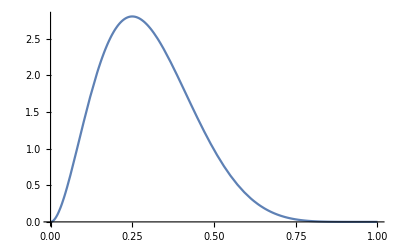

```mathematica
Plot[f1[x],{x,0,1},GridLines->{{m1}, {y1}}]
```

Note that

x+x_1≥2m ⇒ x + f_2^-1[f[x]]≥2m⇒f_2^-1[f[x]]≥2m-x

Since f_2^-1 is decreasing, this is equivalent to

f[x]≥f[2 m-x]

Let

```mathematica
h1=f0[α,β,2 m[α,β] - x]
```

((1+x-(2 (-1+α))/(-2+α+β))^(-1+β) (-x+(2 (-1+α))/(-2+α+β))^(-1+α))/Beta[α,β]

```mathematica
h2=f0[α,β,x]
```

((1-x)^(-1+β) x^(-1+α))/Beta[α,β]

We want the following to be positive

```mathematica
h=h1-h2
```

-((1-x)^(-1+β) x^(-1+α))/Beta[α,β]+((1+x-(2 (-1+α))/(-2+α+β))^(-1+β) (-x+(2 (-1+α))/(-2+α+β))^(-1+α))/Beta[α,β]

To get rid of the powers, we take log of the two terms.

```mathematica
lh=Log[h1]-Log[h2]
```

-Log[((1-x)^(-1+β) x^(-1+α))/Beta[α,β]]+Log[((1+x-(2 (-1+α))/(-2+α+β))^(-1+β) (-x+(2 (-1+α))/(-2+α+β))^(-1+α))/Beta[α,β]]

If this remains positive, then we are good.

```mathematica
lh1=PowerExpand[lh]
```

-(-1+β) Log[1-x]-(-1+α) Log[x]+(-1+β) Log[1+x-(2 (-1+α))/(-2+α+β)]+(-1+α) Log[-x+(2 (-1+α))/(-2+α+β)]

A picture helps.

```mathematica
lh1/.α->3/.β->7
```

2 Log[1/2-x]-6 Log[1-x]-2 Log[x]+6 Log[1/2+x]

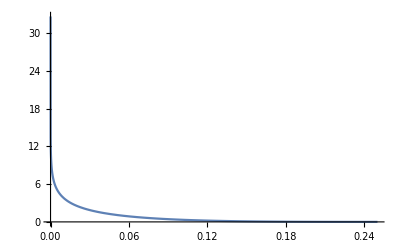

```mathematica
Plot[%,{x,0,m1},PlotRange->Full]
```

Take derivative.

```mathematica
dlh=D[lh1,x]//Simplify
```

(2 (α-β) (1-α+x (-2+α+β))^2)/((-1+x) x (2-2 α+x (-2+α+β)) (-α+β+x (-2+α+β)))

```mathematica
Reduce[dlh<0&&assump,x,Reals]
```

β>1&&1<α<β&&(-1+α)/(-2+α+β)<x1<1&&0<x<(-1+α)/(-2+α+β)

So the derivative is always <0.

And

```mathematica
Limit[lh1,x->0,Assumptions->assump]
```

∞

```mathematica
lh1/.x->m[α,β]
```

0

So there can be only one zero of lh1 on [0,m]. And we are done.